```mathematica
CRCcohortA=Import[NotebookDirectory[]<>"Volume Changes Table - CRC cohort A.csv"]⟦All,1⟧
```

{55,53,47,36,33,27,27,26,22,21,14,9,9,9,8,8,8,7,6,5,4,3,1,0,0,-1,-3,-10,-14,-18,-18,-21,-28,-39,-46,-50,-50,-55,-57,-57,-60,-62,-63,-65,-71,-72,-73,-73,-73,-74,-75,-80,-80,-85,-85,-86,-90,-91,-100}

```mathematica
CRCcohortB=Import[NotebookDirectory[]<>"Volume Changes Table - CRC cohort B.csv"]⟦All,1⟧
```

{90,77,74,71,61,53,50,48,43,40,40,29,22,21,21,20,15,15,15,9,3,2,2,-1,-8,-11,-12,-18,-22,-23,-25,-29,-29,-33,-35,-41,-46,-49,-52,-56,-58,-59,-61,-65,-68,-69,-76,-77,-77,-81,-84,-85,-85,-89,-92,-93,-93,-96,-100,-100,-100,-100}

```mathematica
nonCRC=Import[NotebookDirectory[]<>"Volume Changes Table - nonCRC.csv"]⟦All,1⟧
```

{100,100,100,98,88,81,80,78,74,65,64,63,61,59,57,55,55,52,48,47,46,44,43,41,39,38,37,37,36,36,32,32,31,31,30,30,28,28,27,26,25,24,24,23,23,22,22,22,21,21,21,20,20,20,20,20,19,18,16,16,16,15,15,12,11,10,9,8,8,8,6,5,4,4,4,3,3,3,1,0,-1,-2,-2,-3,-3,-3,-4,-4,-7,-7,-7,-10,-10,-11,-11,-12,-12,-13,-14,-15,-17,-17,-21,-22,-25,-26,-26,-27,-29,-29,-30,-32,-33,-35,-35,-35,-36,-39,-39,-40,-41,-44,-44,-44,-45,-46,-46,-48,-49,-51,-52,-53,-53,-55,-56,-57,-57,-59,-60,-60,-61,-62,-62,-62,-63,-63,-65,-67,-67,-68,-69,-70,-70,-71,-71,-71,-72,-72,-73,-73,-73,-74,-74,-74,-75,-75,-76,-76,-78,-79,-79,-79,-80,-80,-81,-81,-82,-82,-83,-83,-83,-84,-85,-86,-87,-87,-87,-88,-88,-89,-91,-93,-95,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100,-100}

```mathematica
CRCmerged=Reverse[Sort[Join[CRCcohortA,CRCcohortB]]]
```

{90,77,74,71,61,55,53,53,50,48,47,43,40,40,36,33,29,27,27,26,22,22,21,21,21,20,15,15,15,14,9,9,9,9,8,8,8,7,6,5,4,3,3,2,2,1,0,0,-1,-1,-3,-8,-10,-11,-12,-14,-18,-18,-18,-21,-22,-23,-25,-28,-29,-29,-33,-35,-39,-41,-46,-46,-49,-50,-50,-52,-55,-56,-57,-57,-58,-59,-60,-61,-62,-63,-65,-65,-68,-69,-71,-72,-73,-73,-73,-74,-75,-76,-77,-77,-80,-80,-81,-84,-85,-85,-85,-85,-86,-89,-90,-91,-92,-93,-93,-96,-100,-100,-100,-100,-100}

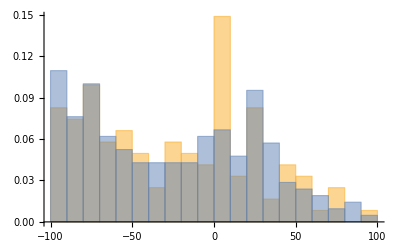

```mathematica
Histogram[{CRCmerged,nonCRC},{-100,100,10},"Probability"]
```

```mathematica
CRCLine=Flatten[Table[{{(i-1)/Length[CRCmerged],CRCmerged⟦i⟧},{(i)/Length[CRCmerged],CRCmerged⟦i⟧}},{i,1,Length[CRCmerged]}],1];
```

```mathematica
nonCRCLine=Flatten[Table[{{(i-1)/Length[nonCRC],nonCRC⟦i⟧},{(i)/Length[nonCRC],nonCRC⟦i⟧}},{i,1,Length[nonCRC]}],1];
```

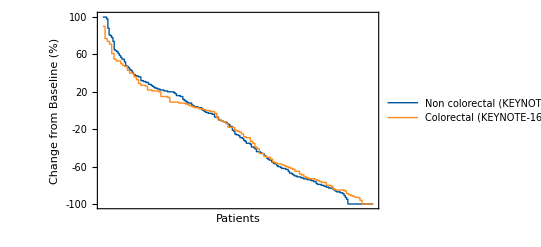

```mathematica
VolumeComparisonPlot=ListPlot[{nonCRCLine,CRCmergedLine},Joined->True,Frame->{{True,False},{True,False}},Axes->{True,False},AxesOrigin->{0,0},FrameStyle->Directive[Black,Thickness[Medium]],PlotRange->{{0,1},{-101,101}},PlotRangePadding->None,Ticks->{None,None},AxesStyle->Directive[Black,Thickness[Medium]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameTicks->{None,Table[{i,i,{0,0.02}},{i,-100,100,20}]},FrameLabel->{"Patients","Change from Baseline (%)"},PlotStyle->{Directive[Darker[ColorData[3,6]],AbsoluteThickness[1]],Directive[Lighter[Orange,0.1],AbsoluteThickness[1]]},PlotLegends->{"Non colorectal\n(KEYNOTE-158)","Colorectal\n(KEYNOTE-164)"},ImageSize->{{340},{1000}}]
```

### fixing exports with plotlegends

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

```mathematica
Export[NotebookDirectory[]<>"CRC and nonCRC volume change comparison.pdf",VolumeComparisonPlot,"PDF"]
```

D:\Dropbox\Palmer, 2016\Her2 neratinib basket trial\New pembrolizumab trials\CRC and nonCRC volume change comparison.pdf